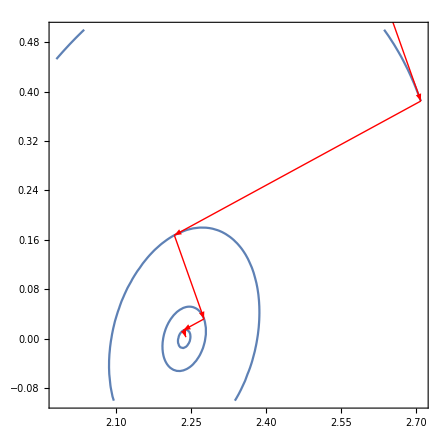

```mathematica
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
str=Import["D:/1/MOVI lab/lab2/lab2/Steepesteps2f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.98,2.71},{y,-0.1,0.5},Mesh->All],{i,1,Length[str]-8}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-8-1}];
Show[K,M]
```

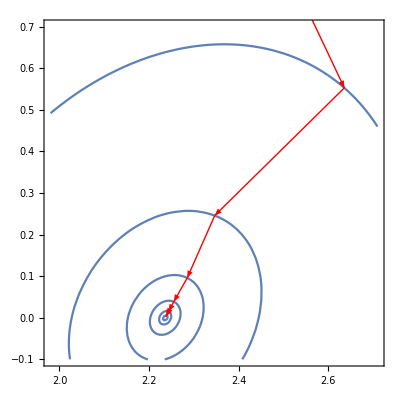

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Spleetingeps2f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.98,2.71},{y,-0.1,0.7},Mesh->All],{i,1,Length[str]-10}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-9-1}];
Show[K,M]
```

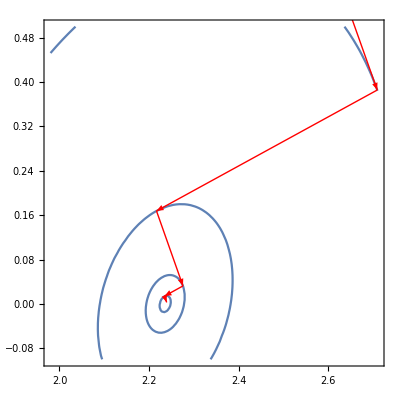

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Steepesteps1f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.98,2.71},{y,-0.1,0.5},Mesh->All],{i,1,Length[str]-3}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-2-1}];
Show[K,M]
```

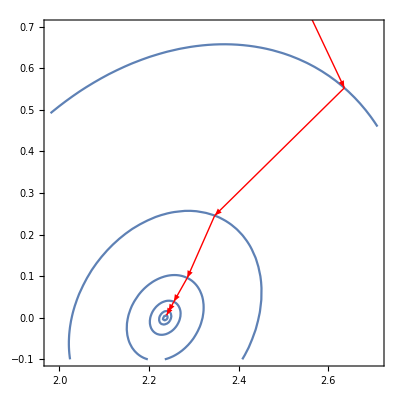

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Spleetingeps1f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.98,2.71},{y,-0.1,0.7},Mesh->All],{i,1,Length[str]-3}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-3-1}];
Show[K,M]
```

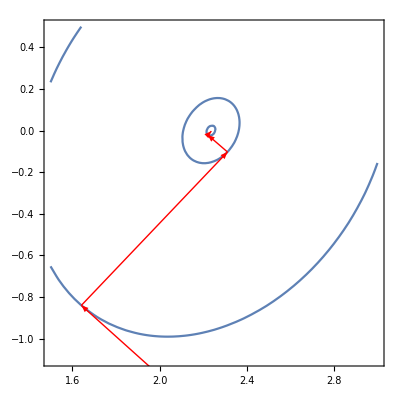

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Steepesteps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.5,3},{y,-1.1,0.5},Mesh->All],{i,1,Length[str]-2}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-1-1}];
Show[K,M]
```

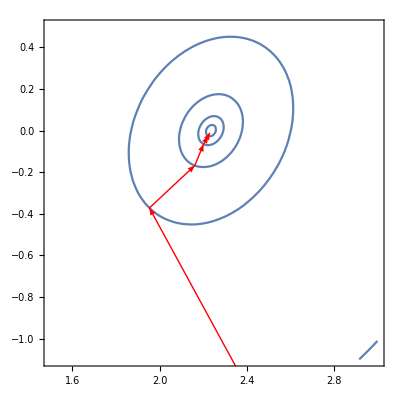

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Spleetingeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.5,3},{y,-1.1,0.5},Mesh->All],{i,1,Length[str]-4}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-3-1}];
Show[K,M]
```

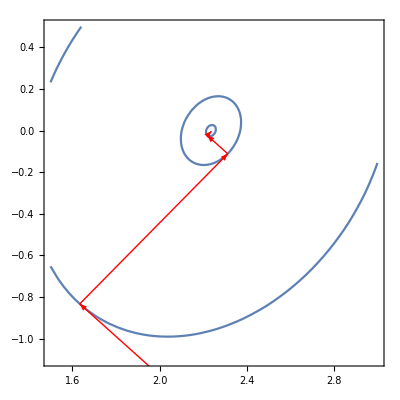

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Steepesteps2f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.5,3},{y,-1.1,0.5},Mesh->All],{i,1,Length[str]-6}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-5-1}];
Show[K,M]
```

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Spleetingeps2f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1.5,3},{y,-1.1,0.5},Mesh->All],{i,1,Length[str]-12}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-11-1}];
Show[K,M]
```

-Graphics-

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Steepesteps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-1.9,2.1},{y,0.9,5.1},Mesh->All],{i,1,Length[str],5}];
L=Table[K[[i]],{i,1,Length[K],5}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-1}];
Show[L,M];
str[[Length[str]]]
```

{1.00866,1.01943}

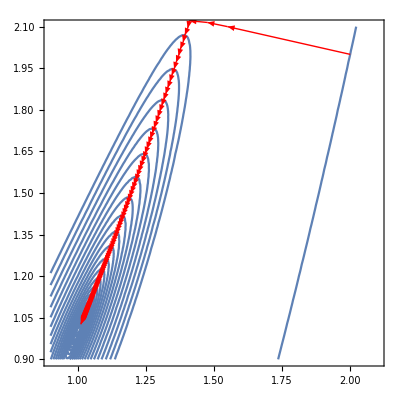

{1.01092,1.02644}

{1.00866,1.01943}

```mathematica
str=Import["D:/1/MOVI lab/lab2/lab2/Spleetingeps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,2.1},Mesh->All],{i,1,Length[str]}];
L=Table[K[[i]],{i,1,Length[K],5}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Arrow[{str[[i]],str[[i+1]]}]}],{i,1,Length[str]-1}];
Show[L,M]
str[[Length[str]]]
```